## classical MB distr

```mathematica
Clear["Global`*"]
(*units and constants for trap depth mostly*)
kHz=10^3;
nm=10^-9;
mK=10^-3;
uK=10^-6;
us=10^-6;
kB=1.38064852 10^-23;
ℏ=1.0545718 10^-34;
amu=1.66054 10^-27;
scale=1;

(*Cs, our expt:*)
λtrap=970 nm;
m=132.90545 amu;
{Ttrap,frad,fax}={.67mK ,√(67/67) 70.7kHz,√(67/67) 11.8kHz};

(*Rb, Grangier:*)
λtrap=810nm;
m=87 amu;
{Ttrap,frad,fax}={1.6mK ,140kHz,30kHz};

(*Rb, Grangier PRA:*)
λtrap=850nm;
m=87 amu;
{Ttrap,frad,fax}={2.8mK ,160kHz,30kHz};

(*Rb, Thompson PRL:*)
λtrap=815nm;
m=87 amu;
{Ttrap,frad,fax}={.82mK ,100kHz,15.6kHz};
scale=.82;

 TList={52,2.4}uK; (*atom temp guesses. assuming: T in uK, and they are in increasing order*)

Utrap = kB Ttrap;
ftrap={frad,frad,fax(*√((λtrap^2 m frad^4)/(2 Utrap))*)} ;
ωtrap=2π ftrap;

w0=√(Utrap/(ftrap[[1]]^2 m π^2)); (*0.67, 133 amu, 71kHz gives 917 nm*)
w[z_]:=w0√(1+((λtrap z)/(π w0^2))^2);
U[r_]:=Utrap(1-w0^2/w[r[[3]]]^2 Exp[-2 (r[[1]]^2+r[[2]]^2)/w[r[[3]]]^2]);
Δt=Range[2,100,5]us;
nSim=10000; (*number of realizations*)


mcTOFfit=Reap[
Do[
Δr=√((kB T)/m)1/ωtrap;
Δv=(*2*)2 √((kB T)/m){1,1,1}; (*why the 2 fudge factor. using MB=Exp[-e/kT]*)

rInit=Transpose[RandomVariate[NormalDistribution[0,#],nSim]&/@Δr];
vInit=Transpose[RandomVariate[NormalDistribution[0,#],nSim]&/@Δv];

KInit=m/2 Norm[#]^2&/@vInit;
PInit=U[#]&/@rInit;
 
(*probability of realization*)

(*MBProb=Exp[-#/(kB T)]/(kB T)&/@(KInit+PInit);
MBProb=2 √(#/π)(1/(kB T))^(3/2)Exp[-#/(kB T)]&/@(KInit+PInit);
MBProb=Exp[-#/(kB T)]&/@(KInit+PInit);
*)
MBProb=2 √(#/π)(1/(kB T))^(3/2)Exp[-#/(kB T)]&/@(KInit+PInit);
(*IF TRUE THEN KEEP (SAMPLE MB DISTR)*)
KeepQ=Positive[#1-#2]&@@{
MBProb,
RandomReal[1,nSim]
};
(*list of positions to keep*)
keep=Flatten[Position[KeepQ,True]];

rInit=rInit[[keep]];
vInit=vInit[[keep]];
KInit=KInit[[keep]];

(*sort by realizations. ie each list scans thru all Δt for a single realization*)
rFin=Transpose[rInit+vInit #&/@Δt];
PFin=U[#]&/@#&/@rFin;

EFin=(#1+#2)&[PFin,KInit];
SurvProb=Thread[{Δt/us,scale Total[#]&/@Transpose[Boole[Positive[Utrap-EFin]]]/Length[keep]}];
(*
sigma=1.Flatten[Differences[#]&/@survErr];
chiSquare=Total[(SurvProb-survival)^2[[;;,2]]/sigma^2];
Sow[{T/uK,SurvProb,chiSquare}]
*)
Sow[{T/uK,SurvProb}]
,{T,TList}]
][[2,1]];

mcTOFfit[[;;,1]]

Show[{
ListPlot[mcTOFfit[[;;,2]],Joined->True,PlotRange->All],
ListPlot[{{10,.5},{20,.2},{40,.5},{70,.2}}]

}
]
```

## thompson prl blue: 10us-->50%, 20 us =20% red: 40us-->50%, 70 us = 20% dont really trust his fit as much. used diff axial temp etc.

{52,2.4}

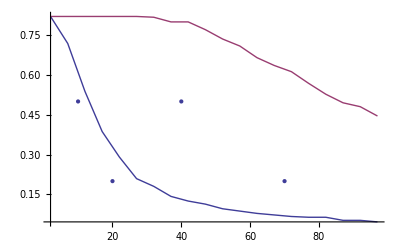

```mathematica
MBProb=Exp[-#/(kB T)]&/@(KInit+PInit);yes factor of 2
```

{52,2.4}

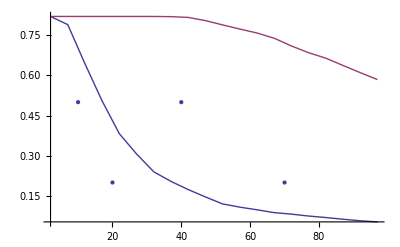

```mathematica
MBProb=Exp[-#/(kB T)]&/@(KInit+PInit); no factor of 2
```

{52,2.4}

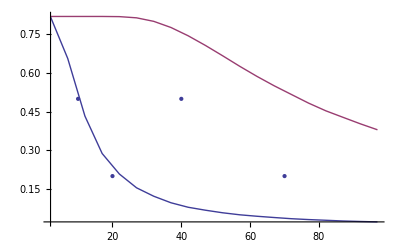

```mathematica
MBProb=2 √(#/π)(1/(kB T))^(3/2)Exp[-#/(kB T)]&/@(KInit+PInit); no factor of 2
```

{52,2.4}

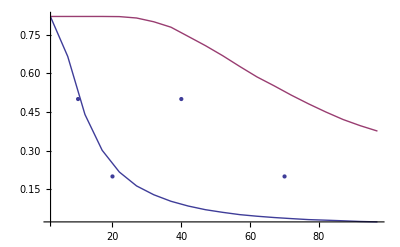

```mathematica
MBProb=Exp[-#/(kB T)]/(kB T)&/@(KInit+PInit); no factor of 2
```

## grangier pra red: 10us-->40%, Blue: 25us-->50%

{31,168}

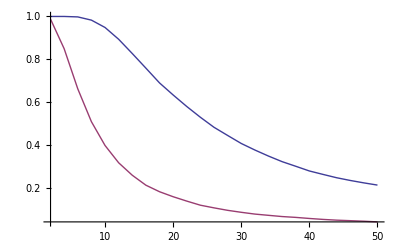

```mathematica
MBProb=Exp[-#/(kB T)]/(kB T)&/@(KInit+PInit); no factor of 2...
```

{31,168}

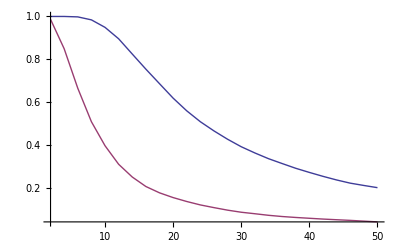

```mathematica
MBProb=2 √(#/π)(1/(kB T))^(3/2)Exp[-#/(kB T)]&/@(KInit+PInit); no factor of 2..
```

{31,168}

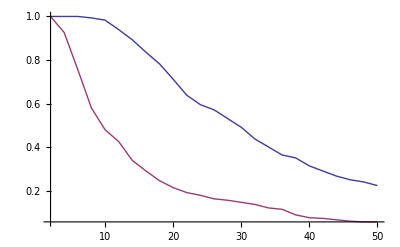

```mathematica
MBProb=Exp[-#/(kB T)]&/@(KInit+PInit);yes factor of 2.
```

{31,168}

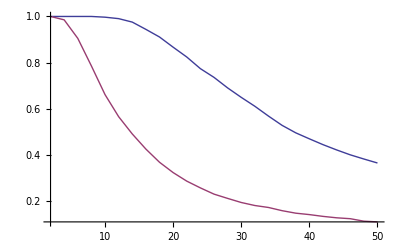

```mathematica
MBProb=Exp[-#/(kB T)]&/@(KInit+PInit);, no factor of 2. NO WAY
```

## grangier--blue: 10us -->40%, red: 20us -->50%

{140,35}

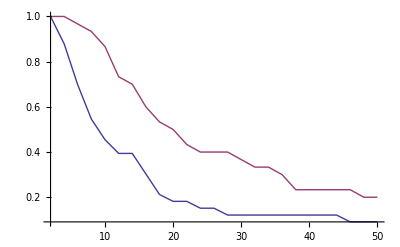

```mathematica
MBProb=Exp[-#/(kB T)]&/@(KInit+PInit);; Grangier. yes factor of 2 could be, but makes no sense.
```

{140,35}

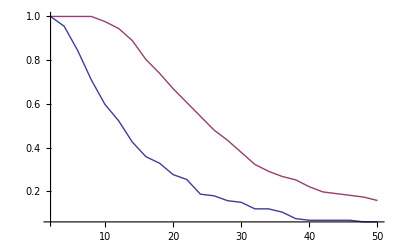

```mathematica
MBProb=Exp[-#/(kB T)]&/@(KInit+PInit);; Grangier. no factor of 2--no fucking way
```

{140,35}

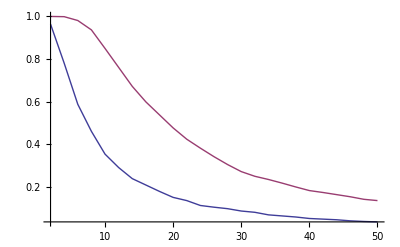

```mathematica
MBProb=2 √(#/π)(1/(kB T))^(3/2)Exp[-#/(kB T)]&/@(KInit+PInit);; Grangier. no factor of 2 --bit better
```

{140,35}

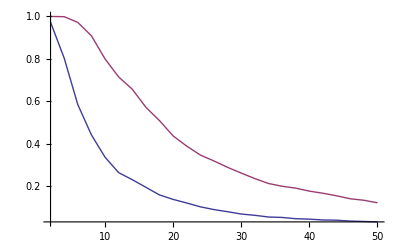

```mathematica
MBProb=Exp[-#/(kB T)]/(kB T)&/@(KInit+PInit);, Grangier. No factor of 2 --a bit worse than above.
```

# different MB distr’s

{1,3,5,7,9,11}

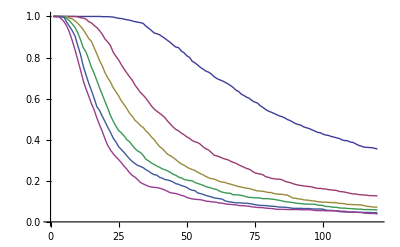

```mathematica
MBProb=2 √(#/π)(1/(kB T))^(3/2)Exp[-#/(kB T)]&/@(KInit+PInit);
```

{1,3,5,7,9,11}

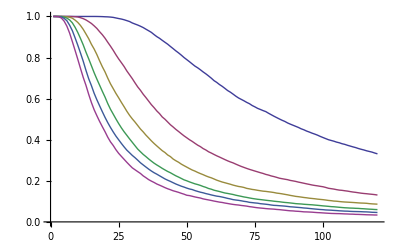

```mathematica
MBProb=#^2/(kB T)^3 Exp[-#/(kB T)]&/@(KInit+PInit);
```

# 670uK

{1,3,5,7,9,11}

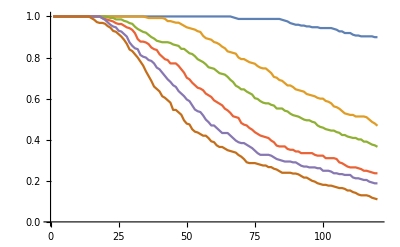

```mathematica
Exp[-#/(kB T)]&/@(KInit+PInit);
```

```mathematica
Integrate[Exp[-e/(k T)]/(k T),{e,0,Infinity}]
```

ConditionalExpression[1,Re[1/(k T)]>0]

```mathematica
Integrate[Exp[-e/(kB T)]/(kB T),{e,0,ee}]
```

1-ⅇ^(-ee/(kB T))

```mathematica
Clear[kB]
Integrate[2 √(e/π)(1/(kB T))^(3/2)Exp[-e/(kB T)],{e,0,ee}]
```

√(1/(kB T)) (-(2 ⅇ^(-ee/(kB T)) √ee)/(√π)+√kB √T Erf[(√ee)/(√kB √T)])